{a→-0.0501369,b→54.5563}

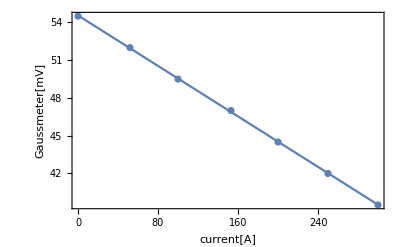

```mathematica
fitfn=a x+b;
params={a,b};
params0={-15/300,55};

mV={54.5,52.0,49.5,47,44.5,42.0,39.5};
A={0,52,100,153,200,250,300};
GvsA=Thread[{A,mV}];

fitGvsA=FindFit[GvsA,fitfn,Thread[{params,params0}],x]
Show[{ListPlot[GvsA,Axes->False,Frame->True,FrameLabel->{"current[A]","Gaussmeter[mV]"},FrameStyle->Large],
Plot[fitfn/.fitGvsA,{x,Min[A],Max[A]}]
}]
```

{a→10.2555,b→54.2601}

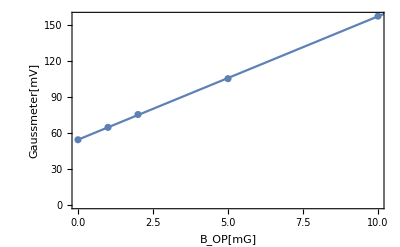

```mathematica
mG={0,1,10,2,5};
mV={54.2,64.5,157,75.2,105};
mGvsmV=Thread[{mG,mV}];

fitmGvsmV=FindFit[mGvsmV,fitfn,Thread[{params,params0}],x]
Show[{ListPlot[Thread[{mG,mV}],Axes->False,Frame->True,FrameLabel->{"B_OP[mG]","Gaussmeter[mV]"},FrameStyle->Large],
Plot[fitfn/.fitmGvsmV,{x,Min[A],Max[A]}]
}]
```

## 300A-->0A: 15.7mG ->0.5mG on display.

```mathematica
10/.05
```

200.